```mathematica
(* constants *)
SubMinus[c] = 6000.;
SubPlus[c]  = 1500.;
SubMinus[ρ] = 3100.;
SubPlus[ρ] = 1000.;
ω = 2100.;

a = (SubMinus[ρ]/SubPlus[ρ])^2;
b = (SubPlus[c]/SubMinus[c])^2;
L0 = 0.;
p0 =√((ω^2 + L0)/SubPlus[c]^2) ;

minDepth[maxModeNum_] := (
minval = First[FindMinimum[{t^2(a (Cot[t])^2 + 1),  Pi (maxModeNum - 1/2) ≤ t ≤ Pi maxModeNum},{t, Pi (maxModeNum - 3/8)}]];
(*err = 0.5; (*addition - to be sure of the global mode existence*) *)
dmin = √(minval/ p0^2(1 - b));
dmin);

bottomHole[x1pos_, x2pos_, bottomDepth_, holeDepth_, holeRad_] := (
shapeFunc[x_] := 0.5 (Cos[Pi x] + 1); (*normalized to 1*)
bottomFunc[x1_, x2_] := Piecewise[{{holeDepth * shapeFunc[(√((x1-x1pos)^2+(x2-x2pos)^2))/holeRad], (x1-x1pos)^2+(x2-x2pos)^2≤holeRad^2}, {0.,True}}] + bottomDepth;
bottomFunc);

λFunc[x1min_, x1max_, x2min_, x2max_, pmax_, bottom_, modeNum_, depth_] := (
(*q[x1_, x2_, p_] := t /.FindRoot[{t^2 (a (Cot[t])^2 + b)== (bottom[x1, x2])^2 p^2 (1 - b)}, {t, Pi (modeNum - 3/8), Pi (modeNum - 1/2), Pi modeNum}];
minval = First[FindMinimum[{t^2(a (Cot[t])^2 + b),  Pi (modeNum - 1/2) ≤ t ≤ Pi modeNum},{t,  Pi (modeNum - 3/8)}]];*)

q[x1_, x2_, p_] := t /.FindRoot[{t^2 (a (Cot[t])^2 + b)== (bottom[x1, x2])^2 p^2 (1 - b)}, {t, 3.14 (modeNum - 3/8), 3.14 (modeNum - 1/2), 3.14 modeNum}];
minval = First[FindMinimum[{t^2(a (Cot[t])^2 + b),  3.14 (modeNum - 1/2) ≤ t ≤ 3.14 modeNum},{t,  3.14 (modeNum - 3/8)}]];

pmin = √(minval/((1 - b) depth^2));
qTab = Table[{{x1, x2, p}, q[x1, x2, p]}, {x1, x1min, x1max, (x1max-x1min)/20}, {x2, x2min, x2max, (x2max-x2min)/20}, {p, pmin, pmax, (pmax-pmin)/20}];
qTabFlat = Flatten[qTab, 2];
qFunc= Interpolation[qTabFlat];
λ[x1_, x2_, p_]:= qFunc[x1, x2, p]/bottom[x1, x2];
λ);

getTrajAndPhaseAndJac[x1in_, x2in_, λFunc_, timeTo_] :=(
λ := λFunc;
Subscript[p, abs] := Sqrt[p0^2 - (λ[x1in, x2in, p0])^2];
L[x1_, x2_, p_] := ((SubPlus[c])^2((λ[x1, x2, p])^2 + p^2) - ω^2);
Lp[x1_, x2_, p_]:= Evaluate[D[L[x1, x2, p], {p, 1}]];
Lx1[x1_, x2_, p_]:= Evaluate[D[L[x1, x2, p], {x1, 1}]];
Lx2[x1_, x2_, p_]:= Evaluate[D[L[x1, x2, p], {x2, 1}]];
{x1sol, x2sol,p1sol, p2sol} =ParametricNDSolve[{Subscript[x, 1]'[t]== Lp[Subscript[x, 1][t], Subscript[x, 2][t], √((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2)] (Subscript[p, 1][t])/(√((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2)),
Subscript[x, 2]'[t]== Lp[Subscript[x, 1][t], Subscript[x, 2][t], √((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2)] (Subscript[p, 2][t])/(√((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2)),
Subscript[p, 1]'[t]== -Lx1[Subscript[x, 1][t], Subscript[x, 2][t], √((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2)],
Subscript[p, 2]'[t]==-Lx2[Subscript[x, 1][t], Subscript[x, 2][t], √((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2)],
Subscript[x, 1][0]==x1in, Subscript[x, 2][0]==x2in, Subscript[p, 1][0]==Subscript[p, abs] Cos[θ], Subscript[p, 2][0] == Subscript[p, abs] Sin[θ]},
{Subscript[x, 1], Subscript[x, 2], Subscript[p, 1], Subscript[p, 2]},{t,0.,timeTo},{θ}];


Subscript[x, 1][θ_, t_] := (Subscript[x, 1][θ]/.x1sol)[t];
Subscript[x, 2][θ_, t_] := (Subscript[x, 2][θ]/.x2sol)[t];
Subscript[p, 1][θ_, t_] := (Subscript[p, 1][θ]/.p1sol)[t];
Subscript[p, 2][θ_, t_] := (Subscript[p, 2][θ]/.p2sol)[t];

(*Subscript[dx, 1][θ_, t_] := Lp[Subscript[x, 1][θ, t], Subscript[x, 2][θ, t], √((Subscript[p, 1][θ, t])^2 + (Subscript[p, 2][θ, t])^2)] (Subscript[p, 1][θ, t])/(√((Subscript[p, 1][θ, t])^2 + (Subscript[p, 2][θ, t])^2));

Subscript[dx, 2][θ_, t_] := Lp[Subscript[x, 1][θ, t], Subscript[x, 2][θ, t], √((Subscript[p, 1][θ, t])^2 + (Subscript[p, 2][θ, t])^2)] (Subscript[p, 2][θ, t])/(√((Subscript[p, 1][θ, t])^2 + (Subscript[p, 2][θ, t])^2));*)
Subscript[dx, 1][θ_, t_] := Evaluate[D[Subscript[x, 1][θ, t], {t, 1}]];

Subscript[dx, 2][θ_, t_] := Evaluate[D[Subscript[x, 2][θ, t], {t, 1}]];

phase[θ_, t_] := Integrate[Subscript[p, 1][θ, tau] Subscript[dx, 1][θ, tau] + Subscript[p, 2][θ, tau] Subscript[dx, 2][θ, tau], {tau, 0., t}(*, Assumptions->t∈Reals*)];
(*phaseTab:= Table[{{Subscript[x, 1][θ, t], Subscript[x, 2][θ, t]}, phaseManifold[θ, t]}, {θ, 0.05, 2Pi, Pi/2}, {t, 0.0000001, timeTo, (timeTo - 0.0000001)/5}];
phaseTabFlat = Flatten[phaseTab, 1];
phase= Interpolation[phaseTabFlat];*)
Subscript[dthx, 1][θ_, t_] := Evaluate[D[Subscript[x, 1][θ, t], {θ, 1}]];

Subscript[dthx, 2][θ_, t_] := Evaluate[D[Subscript[x, 2][θ, t], {θ, 1}]];
jac[θ_, t_]:= Abs[Subscript[dthx, 1][θ, t]Subscript[dx, 2][θ, t] - Subscript[dthx, 2][θ, t] Subscript[dx, 1][θ, t]];
{Subscript[x, 1], Subscript[x, 2], Subscript[p, 1], Subscript[p, 2], phase, jac});

points[timeTo_, x1_, x2_, phaseFunc_, phaseVal_, pointsNum_] :=(
timeVal[θ_] := t /.FindRoot[{phaseFunc[θ, t]== phaseVal}, {t, 0., 0., timeTo}];
pts = Table[{x1[θ, timeVal[θ]], x2[θ, timeVal[θ]]},{θ, (2 Pi)/pointsNum, 2 Pi, (2 Pi)/pointsNum}];
pts);

(*pointsTab[] :=(
);*)
jacFunc[x1_, x2_, jac_, timeTo_] :=(
jacTab:= Table[{{x1[θ, t], x2[θ, t]}, jac[θ, t]}, {θ, Pi/40, 2Pi, Pi/40}, {t,0.05 timeTo, timeTo, (0.95 timeTo)/40}];
jacTabFlat = Flatten[jacTab, 1];
jFunc= Interpolation[jacTabFlat];
jFunc);
(*----------------------------------------------------------------------*)
```

```mathematica
x1min = -6.;
x1max = 8.;
x2min = -6.;
x2max = 6.;
pmax = p0;
holeDepth = 2.;
holeRad = 0.1 holeDepth;
maxModeNum = 2;
bottomDepth = minDepth[maxModeNum];
bottomFunc[x1_, x2_] := bottomDepth + 2 (ArcTan[x1/(0.2 Pi)] + Pi/2.1);
modeNum = 2;
depth = bottomDepth;
λ = λFunc[x1min, x1max, x2min, x2max, pmax, bottomFunc, modeNum, depth];

x2in = 0.;
x1in = 0.5;
timeTo= 0.0000015;
{Subscript[x, 1], Subscript[x, 2], Subscript[p, 1], Subscript[p, 2], ph, j}= getTrajAndPhaseAndJac[x1in, x2in,λ, timeTo];
(*----------------------------------------------------------------------*)
```

InterpolatingFunction::dmval: Input value {8.08162,2.13449,1.27226} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

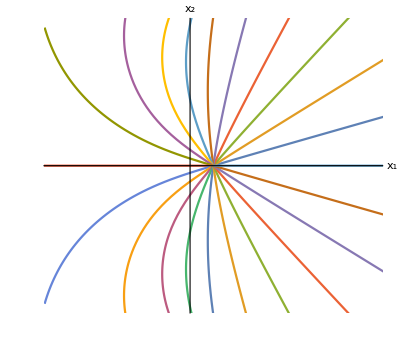

```mathematica
Show[ParametricPlot[Evaluate@Table[{Subscript[x, 1][θ,t], Subscript[x, 2][θ, t]}, {θ,Pi/11,2Pi, Pi/11}], {t, 0. , timeTo}, PlotRange->{{-3., 4.},{-3., 3.}}, Ticks->None, AxesLabel->{Style["x_1", FontSize->18], Style["x_2", FontSize->18]}]]
```

```mathematica
newPh[θ_, t_]:= 10 ph[θ,t];
pts1 = points[timeTo, Subscript[x, 1], Subscript[x, 2], newPh, 1 Pi 5/2, 25];
pts2 = points[timeTo, Subscript[x, 1], Subscript[x, 2], newPh, 2Pi 5/2, 25];
pts3 = points[timeTo, Subscript[x, 1], Subscript[x, 2], newPh, 3Pi 5/2, 25];
pts4 = points[timeTo, Subscript[x, 1], Subscript[x, 2], newPh, 4Pi 5/2, 25];
pts5 = points[timeTo, Subscript[x, 1], Subscript[x, 2], newPh, 5Pi 5/2, 25];
pts6 = points[timeTo, Subscript[x, 1], Subscript[x, 2], newPh, 6Pi 5/2, 25];
```

InterpolatingFunction::dmval: Input value {8.14921,1.88441,1.2723} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::reged: The point {1.5×10^-6} is at the edge of the search region {0.,1.5×10^-6} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::reged: The point {1.5×10^-6} is at the edge of the search region {0.,1.5×10^-6} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

```mathematica
pts1pi
```

{{0.499974,0.000044752},{0.499974,-0.000044752},{0.500052,0.}}

```mathematica
Show[ParametricPlot[Evaluate@Table[{Subscript[x, 1][θ,t], Subscript[x, 2][θ, t]}, {θ,Pi/11,2Pi, Pi/11}], {t, 0. , timeTo}, PlotRange->{{-5., 3.},{-3., 3.}}, Ticks->None, AxesLabel->{Style["x_1", FontSize->22], Style["x_2", FontSize->22]}],
Graphics[{(*Thick,*) Dashed, BSplineCurve[pts1,SplineClosed->True]}],
Graphics[{(*Thick,*) Dashed, BSplineCurve[pts2,SplineClosed->True]}],
Graphics[{(*Thick,*) Dashed, BSplineCurve[pts3,SplineClosed->True]}],
Graphics[{(*Thick,*) Dashed, BSplineCurve[pts4,SplineClosed->True]}]
(*Graphics[{Thick, Dashed, BSplineCurve[pts5,SplineClosed->True]}],
Graphics[{Thick, Dashed, BSplineCurve[pts6,SplineClosed->True]}]*)]
```

-Graphics-

```mathematica
jac = jacFunc[Subscript[x, 1], Subscript[x, 2], j, timeTo];
```

InterpolatingFunction::dmval: Input value {8.0808,0.573756,1.27226} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
Plot3D[1/jac[x1, x2], {x1, -5., 5.}, {x2, -3., 3.}, PlotRange->All,ColorFunction->(ColorData["TemperatureMap"][#3]&), Ticks->None]
```

-Graphics3D-